```mathematica
A=({{1, 3, 2}, {4, 2, 1}, {0, 3, 2}});
cp=Det[A-λ*IdentityMatrix[Length[A]]]
```

1+7 λ+5 λ^2-λ^3

```mathematica
(*end of 1(i)*)
Solve[cp==0,λ]
```

{{λ→-1},{λ→3-√10},{λ→3+√10}}

```mathematica
(*end of 1 ii*)
IdentityMatrix[Length[A]]+7*A+5*MatrixPower[A,2]-MatrixPower[A,3]
```

{{0,0,0},{0,0,0},{0,0,0}}

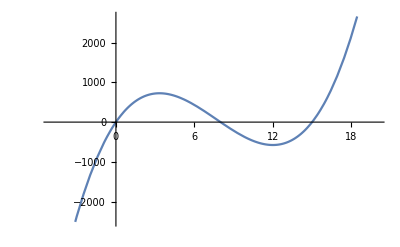

```mathematica
(*end of 1 iii*)
Clear[f]
f[x_]=480*x-92*x^2+4*x^3;
b=Plot[f[x],{x,-5,20}]
```

```mathematica
(*end of 2 i*)
cri=Solve[f'[x]==0]//N
```

{{x→3.33333},{x→12.}}

```mathematica
{f'[1],f'[6],f'[20]}
```

{308,-192,1600}

```mathematica
(*f is increasing in the open interval (-∞,3.33) and (12,∞) and decreasing in the open interval (3.33,12)*)
(*end of 2 ii*)
inf=Solve[f''[x]==0]//N
```

{{x→7.66667}}

```mathematica
{f''[7],f''[8]}
```

{-16,8}

```mathematica
(*f is concave up on the open interval (7.6667,∞) and concave down on the open interval (-∞,7.6667)*)
(*end of  2 iii*)
FindMaximum[f[x],{x,5}]
FindMinimum[f[x],{x,12}]
```

{725.926,{x→3.33333}}

{-576.,{x→12.}}

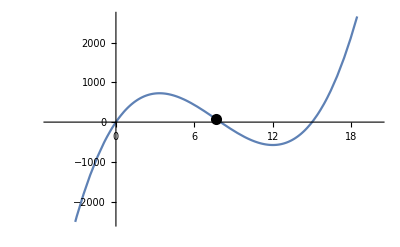

```mathematica
(*end of 2 iv*)
p=inf[[1,1,2]];
a=Graphics[{PointSize[0.02],Point[{p,f[p]}]}];
Show[b,a]
```

```mathematica
(*end of 2 v*)
Clear[a,b,c,h,g,f,x,y,X,Y]
(*Given equation of Conic*)
p:=32*x^2+52*x*y-7*y^2-64*x-52*y-148
(*Comparing with the general equation of 2nd degree*)
a=32;b=-7;c=-148;
h=26;g=-32;f=-26;
(*Calculating parameter*)
d1=Det[({{a, h, g}, {h, b, f}, {g, f, c}})]
d2=a*b-h^2
d3=a+b
```

162000

-900

25

```mathematica
(*Since d1≠0,d2<0 and d3≠0, the equation represent a hyperbola*)
α=(f h-b g)/d2;
β=(g h-a f)/d2;
θ=(1/2)ArcTan[2*h/(a-b)];
(*Rotating the axes by angel θ and shifting the center to {α,β} to remove xy terms and x,y terms respectively*)
P=Expand[p/.x->X*Cos[θ]-Y*Sin[θ]+α/.y->X*Sin[θ]+Y*Cos[θ]+β//Simplify]
```

-180+45 X^2-20 Y^2

hence the equation be,
            45 X^2-20 Y^2-180=0;
=>45 X^2-20 Y^2=180;
=>(45 X^2-20 Y^2)/180=1;
=>X^2/4-Y^2/9=1;
Which is the standard form of the conic

```mathematica
(* Computiong the equation of transformed axes with respect to original axes*)
var=Expand[Solve[x==X*Cos[θ]-Y*Sin[θ]+1&&y==X*Sin[θ]+Y*Cos[θ],{X,Y}]]//N
```

{{X→-0.894427+0.894427 x+0.447214 y,Y→0.447214-0.447214 x+0.894427 y}}

```mathematica
X1=var[[1,1,2]];
Y1=var[[1,2,2]];
(*Comparing X^2/4-Y^2/9=1 with the standard equation of hyperbola*)
A=2;
B=3;
e=Sqrt[1-(A^2/B^2)];
(*focus of the Hyperbola*)
p1=Solve[X1==A*e&&Y1==0,{x,y}]
p2=Solve[X1==-A*e&&Y1==0,{x,y}]
```

{{x→2.33333,y→0.666667}}

{{x→-0.333333,y→-0.666667}}

```mathematica
(*equation of the axes*)
Solve[X1==0,y]//Expand
Solve[Y1==0,y]//Expand
```

{{y→2.-2. x}}

{{y→-0.5+0.5 x}}

```mathematica
(*latus rectum*)
Solve[X1==A*e,y]
Solve[X1==-A*e,y]
```

{{y→2.23607 (2.38514-0.894427 x)}}

{{y→2.23607 (-0.596285-0.894427 x)}}

```mathematica
(*Directrix*)
Solve[X1==A/e,y]
Solve[X1==-A/e,y]
```

{{y→2.23607 (3.57771-0.894427 x)}}

{{y→2.23607 (-1.78885-0.894427 x)}}

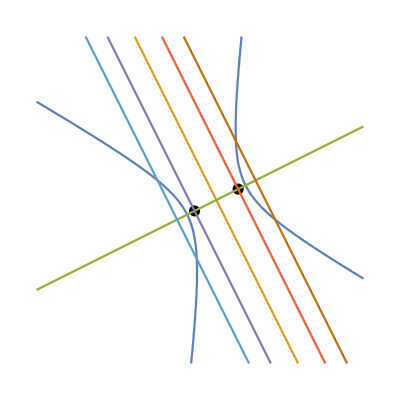

```mathematica
(*sketch*)
bb=Graphics[{PointSize[0.02],{Point[{p1[[1,1,2]],p1[[1,2,2]]}],Point[{p2[[1,1,2]],p2[[1,2,2]]}]}}];
dd=ContourPlot[{p==0,X1==0,Y1==0,X1==A*e,X1==-A*e,X1==A/e,X1==-A/e},{x,-10,10},{y,-10,10}];
Show[bb,dd]
```

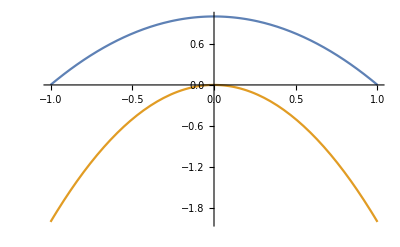

```mathematica
(*end of 3*)
Clear[f,g,x,y]
f=1-x^2;
g=x^2-3 x^2;
Plot[{f,g},{x,-1,1}]
```

```mathematica
Find[f-g==0,x]
```

Find::stream: 1+x^2==0 is not a string, SocketObject, InputStream[ ], or OutputStream[ ].

$Failed

```mathematica
(*end of 4 a*)
Det[({{x, y, z, 1}, {4, 1, 0, 1}, {2, -3, 4, 1}, {1, 0, 0, 1}})]==0
```

-4+4 x-12 y-10 z==0

```mathematica
(*end of 4 b*)
```

```mathematica
∑_(i=1)^∞ 1/(i*(i+1))
```

1

```mathematica
sum=0;
Do[sum=sum+1/(i*(i+1)),{i,1,n}]
sum
```

```mathematica
s=0;
i=1;
While[i≤n,s=s+1/(i*(i+1));i++]
s
```

0

```mathematica
For[s=0;i=1,i≤n,i++,s=s+1/(i*(i+1))]
```

```mathematica
(*end of 5 a*)
```

```mathematica
a=Sum[ArcTan[1/(3+4*(j-1)+2*(j-1)*(j-2)/2)],{j,1,n}]
Limit[a,n->∞]
```

-π/4+ArcTan[1+n]

π/4

```mathematica
(*end of 5 b*)

For[i=1;set={},Fibonacci[i]≤1500,i++,If[PrimeQ[Fibonacci[i]],set=AppendTo[set,Fibonacci[i]]]]
set
Length[set]
```

{2,3,5,13,89,233}

6

```mathematica
(*end of 5 c*)
n=123;
l1=Range[n]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123}

```mathematica
l2={};
Do[If[Divisible[l1[[i]],7],If[Divisible[l1[[i]],3],Continue,l2=AppendTo[l2,l1[[i]]]]],{i,Length[l1]}]
l2
```

{7,14,28,35,49,56,70,77,91,98,112,119}

```mathematica
l3={};
Do[If[PrimeQ[l2[[i]]],l3=Append[l3,l2[[i]]]],{i,Length[l2]}]
l3
```

{7}

```mathematica
Union[l1,l2]
Intersection[l1,l2]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123}

{7,14,28,35,49,56,70,77,91,98,112,119}

```mathematica
(*End of set B*)
(*thanks everyone for Disturbing*)
```

```mathematica
Standar
```